```mathematica
ClearAll["Global`*"]
```

```mathematica
GenDeltaSBot[i_,S_,kin_,Conn_,ProbSnegPrey_]:=kin*2*(S-1)*Conn*Subscript[η, i]*(1-2*ProbSnegPrey);
GenDeltaSTop[i_,S_,kout_,Conn_,ProbSnegPred_]:=kout*2*(S-1)*Conn*(1-Subscript[η, i])*(1-2*ProbSnegPred);
GenDeltaSTopPredPlus[i_,S_,kout_,Conn_,ProbSnegPred_]:=kout*(1 + (2*(S-1)*Conn*(1-Subscript[η, i]) - 1)*(1-2*ProbSnegPred));
GenDeltaSTopPredMinus[i_,S_,kout_,Conn_,ProbSnegPred_]:=kout*(-1 + (2*(S-1)*Conn*(1-Subscript[η, i]) - 1)*(1-2*ProbSnegPred));
BetaFromMeanVariance[etaMean_,etaVar_]:=Module[{alpha,beta},
alpha=etaMean*((etaMean*(1-etaMean)/etaVar)-1);
beta=(1-etaMean)*((etaMean*(1-etaMean)/etaVar)-1);
BetaDistribution[alpha,beta]];
(*GenDeltaSBot = kin*2*(S-1)*Conn*Subscript[η, i]*(1-2*(ProbSnegPrey));*)
(*GenDeltaSTop =  kout*2*(S-1)*Conn*(1-Subscript[η, i])*(1 - 2*(ProbSnegPred));*)
S=100;
Conn=0.02;
kin=5;
kout=10;
g=10;
maxi = 10;
nicheint = 1/(maxi-1);
(*nichevalues =N[Table[i,{i,1/maxi,(maxi-nicheint)/maxi,nicheint}]]*)
nichevalues =N[Table[i,{i,0,1,nicheint}]]
maxi=Length[nichevalues];
PredEta = Subscript[η, i]+nicheint;
(*EtaDiv = 2;*) (*From earlier Zeno idea*)
(*PredEta = (Subscript[η, i]+1)/EtaDiv; *)
(*PreyEta = EtaDiv*Subscript[η, i] - 1;*)
(*For saving future values*)
ProbSneg =Table[0,{maxi}];
ProbSnegPredPlus=Table[0,{maxi}];
ProbSnegPredMinus=Table[0,{maxi}];
ProbSnegvalues=Table[0,{maxi}];
ProbSnegExpectation=Table[0,{maxi}];
ProbSnegExpectation2 = Table[0,{maxi}];
cascadevalue = Table[0,{maxi}];
ExpectedCascade = Table[0,{maxi}];
```

{0.,0.111111,0.222222,0.333333,0.444444,0.555556,0.666667,0.777778,0.888889,1.}

```mathematica
Table[
If[i==1,
DeltaSBot=g,
(*Put prior ProbSneg functions in terms of Subscript[η, i]*)
ProbSnegPreyList = Table[
x = i-j;
ProbSneg[[j]]/.Subscript[η, j]->(Subscript[η, i]-(i-j)*nicheint),(*Even intervals only*)
(*ProbSneg[[j]]/.{Subscript[η, x]->2^x*Subscript[η, i]-(2^x-1)},*) (*Xeno only*)
{j,1,i-1}];
ProbSnegPrey=(1/(i-1))*Sum[ProbSnegPreyList[[j]],{j,1,i-1}];(*Average all ProbSneg from lower trophic levels*)
DeltaSBot=GenDeltaSBot[i,S,kin,Conn,ProbSnegPrey]
];
(*ProbSnegPred=(1-Subscript[η, i+1]);*)
(*This one ranges from beta to 1-beta*)
(*ProbSnegPred = ( 1-Subscript[η, i+1]+β*(2*Subscript[η, i+1]-1))/.β->0.38;*)
(*ProbSnegPred = 0.1;*)(*(0.4)*(Subscript[η, i+1]) + 0.1;*)
(*ProbSnegPred =0.5+0.1* Log[Subscript[η, i+1]/(1-Subscript[η, i+1])];*)
(*This one ranges from beta to 0.5*)
(*ProbSnegPred =(0.55+(-0.55+β) (1-Subscript[η, i+1]))/.β->0.45;*)
ProbSnegPred = 0.47;
DeltaSTop=GenDeltaSTop[i,S,kout,Conn,ProbSnegPred];
DeltaSTopPredPlus=GenDeltaSTopPredPlus[i,S,kout,Conn,ProbSnegPred];
DeltaSTopPredMinus=GenDeltaSTopPredMinus[i,S,kout,Conn,ProbSnegPred];
(*Distribution across niche axis*)
(*If at top of niche axis, there is no top-down effect*)
If[i==maxi,
ProbSneg[[i]]= 1 - 1/(1+Exp[-(DeltaSBot- DeltaSTop)])/.{Subscript[η, i+1]->1};
ProbSnegPredPlus[[i]]= 1 - 1/(1+Exp[-(DeltaSBot- DeltaSTopPredPlus)])/.{Subscript[η, i+1]->1};
ProbSnegPredMinus[[i]]= 1 - 1/(1+Exp[-(DeltaSBot- DeltaSTopPredMinus)])/.{Subscript[η, i+1]->1};
,
ProbSneg[[i]]= 1 - 1/(1+Exp[-(DeltaSBot- DeltaSTop)])/.{Subscript[η, i+1]->PredEta};
ProbSnegPredPlus[[i]]= 1 - 1/(1+Exp[-(DeltaSBot- DeltaSTopPredPlus)])/.{Subscript[η, i+1]->PredEta};
ProbSnegPredMinus[[i]]= 1 - 1/(1+Exp[-(DeltaSBot- DeltaSTopPredMinus)])/.{Subscript[η, i+1]->PredEta};
];
(*Assume niche value take on exact interval value*)
ProbSnegvalues[[i]] = ProbSneg[[i]]/.Subscript[η, i]->nichevalues[[i]];
(*Assume niche value varies uniformally*)
Quiet[ProbSnegExpectation[[i]]=NIntegrate[ProbSneg[[i]],{Subscript[η, i],0,1}]];
(*Assume niche value varies with Beta Dist*)
If[i==1 ,
meaneta = 0.001,
If[i==maxi,
meaneta=0.999,
meaneta = nichevalues[[i]]]
];
(*Variance: constant? Or near-max?*)
(*vareta = 0.08;*)
vareta = (meaneta*(1-meaneta))*(0.1);(*Variance increases in the middle; declines at ends*)
dist=BetaFromMeanVariance[meaneta,vareta];
Quiet[ProbSnegExpectation2[[i]]=NIntegrate[PDF[dist,Subscript[η, i]]*ProbSneg[[i]],{Subscript[η, i],0,1}]];
(*Calculate Cascades*)
cascadevalue[[i]] = Log[(2 + (1)*(1 -ProbSnegPredPlus[[i]]) + (-1)*ProbSnegPredPlus[[i]])/(2 + (1)*(1 - ProbSnegPredMinus[[i]]) + (-1)*ProbSnegPredMinus[[i]])];
Quiet[ExpectedCascade[[i]]=NIntegrate[PDF[dist,Subscript[η, i]]*cascadevalue[[i]],{Subscript[η, i],0,1}]];
,{i,1,maxi}];
```

```mathematica
GraphicsRow[{
Show[{
ListPlot[Transpose[{nichevalues,ProbSnegvalues}],Joined->True,Frame->True,FrameLabel->{"Niche Value","Prob S-"},PlotRange->{0,All}],
ListPlot[Transpose[{nichevalues,ProbSnegvalues}],Joined->False]}],
If[Conn==0.02,
trophiclevelparams = {A->1.00,B->1.956,alpha->0.74},
If[Conn==0.04,
trophiclevelparams ={A->1, B->2.501,alpha->0.582}(*{A->0.895,B->2.594,alpha->0.540}*),
If[Conn==0.1,
trophiclevelparams = {A->0.76,B->3.921,alpha->0.406}]
]
];
trophiclevels = A+B*nichevalues^alpha/.trophiclevelparams;
Show[{
ListPlot[Transpose[{trophiclevels,ProbSnegvalues}],Joined->True,Frame->True,FrameLabel->{"Trophic level","Prob S-"},PlotRange->{0,All}],
ListPlot[Transpose[{trophiclevels,ProbSnegvalues}],Joined->False]}],
Show[{
ListPlot[Transpose[{trophiclevels,ProbSnegExpectation}],Joined->True,Frame->True,FrameLabel->{"Trophic level","E{Prob S-}"},PlotRange->{-0.01,1}],
ListPlot[Transpose[{trophiclevels,ProbSnegExpectation}],Joined->False]}],
Show[{
ListPlot[Transpose[{nichevalues,ProbSnegExpectation2}],Joined->True,Frame->True,FrameLabel->{"Niche Value","E{Prob S-}"},PlotRange->{-0.01,1}],
ListPlot[Transpose[{nichevalues,ProbSnegExpectation2}],Joined->False]}],
Show[{
ListPlot[Transpose[{trophiclevels,ProbSnegExpectation2}],Joined->True,Frame->True,FrameLabel->{"Trophic level","E{Prob S-}"},PlotRange->{-0.01,1}],
ListPlot[Transpose[{trophiclevels,ProbSnegExpectation2}],Joined->False]}]
}]
```

-Graphics-

```mathematica
datapropneg = Import[StringJoin[$HomeDirectory,"/Dropbox/PostDoc/2024_trophicspinglass/trophicspinglass/data/n_c_propneg_data_g10_kout10.csv"]];
```

```mathematica
ConnValues = {0.02,0.02};
(*m1values = {0.036,0.14};
m2values = {1.2,0.14};*)
{sampledData,sampledDataSD}=Table[
Cvalue = ConnValues[[i]];
datasubset=Select[datapropneg[[2;;]],#[[2]]==Cvalue&][[All,{6,3}]];
datasubsetSD=Select[datapropneg[[2;;]],#[[2]]==Cvalue&][[All,{6,7}]];
len=Length[datasubset];
sampleCount=50;
(*Generate 100 evenly spaced indices from 1 to len*)
indices=Round[Subdivide[1,len,sampleCount-1]];
(*Get the sampled subset*)
sampledset = datasubset[[indices]];
sampledsetSD = datasubsetSD[[indices]];
(*TL =1 + 11.6*(sampledset[[;;All,1]]*Cvalue)^0.49;*)
(*Transpose[{TL,sampledset[[;;All,2]]}]*)
{Transpose[{sampledset[[;;All,1]],sampledset[[;;All,2]]}],Transpose[{sampledsetSD[[;;All,1]],sampledsetSD[[;;All,2]]}]}
,{i,1,Length[ConnValues]}];
```

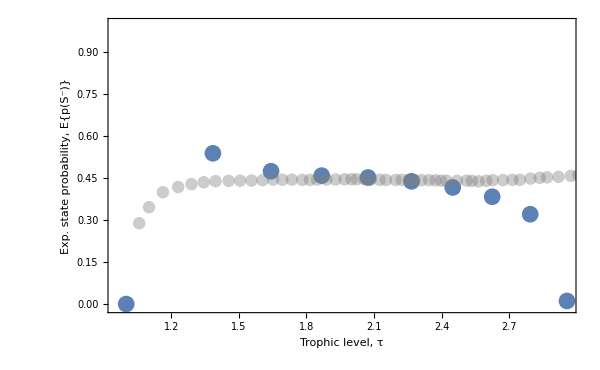

```mathematica
ExpectedProbNegPlot = Show[{
ListPlot[Transpose[{trophiclevels,ProbSnegExpectation2}],PlotStyle->{ColorData[97,1],PointSize[0.02]},Joined->False,Frame->True,FrameLabel->{Style["Trophic level, τ",FontFamily->"Times New Roman",FontSize->18],Style["Exp. state probability, E{p(S^-)}",FontFamily->"Times New Roman",FontSize->18]},PlotRange->{-0.01,1},LabelStyle->Directive[FontSize->16,Black]],
(*ListPlot[Transpose[{trophiclevels,ProbSnegExpectation2}],Joined->False],*)
ListPlot[sampledData[[1]],PlotStyle->Directive[Opacity[0.4],Gray,PointSize[0.015]],Joined->False,PlotRange->All]
(*,
ListPlot[SDPlus,PlotStyle->{Gray,PointSize[0.02]},Joined->True,PlotRange->All],
ListPlot[SDMinus,PlotStyle->{Gray,PointSize[0.02]},Joined->True,PlotRange->All]*)
},
ImageSize->600]
```

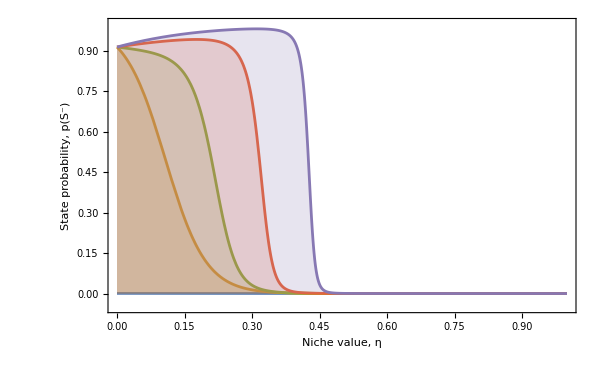

```mathematica
maxdist = 5;
ExpectedProbNegDistPlot=Show[
Table[
Plot[ProbSneg[[k]]/.Table[Subscript[η, j]->Subscript[η, i],{j,1,maxdist}],{Subscript[η, i],0,1},PlotRange->{-0.05,1},Filling->Axis,PlotStyle->ColorData[97,k],Frame->True,FrameLabel->{Style["Niche value, η",FontFamily->"Times New Roman",FontSize->18],Style["State probability, p(S^-)",FontFamily->"Times New Roman",FontSize->18]},LabelStyle->Directive[FontSize->16,Black]],{k,1,maxdist}],ImageSize->600
]
```

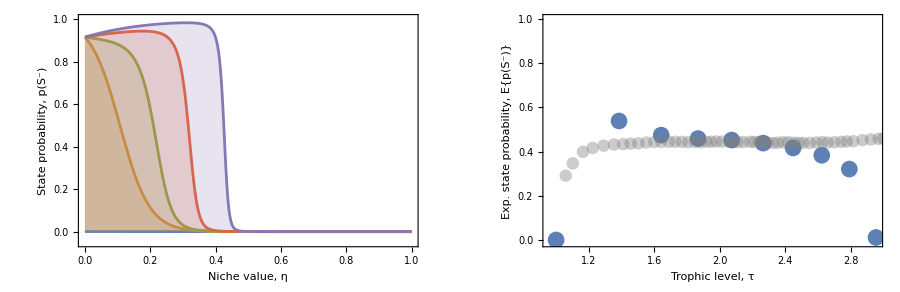

```mathematica
ExpectedProbNeg2PanelPlot = GraphicsRow[{ExpectedProbNegDistPlot,ExpectedProbNegPlot},ImageSize->900]
```

```mathematica
filename = StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2024_trophicspinglass/trophicspinglass/figures_prefinal/fig_expectedprobneg_2panel.pdf"}];
Export[filename,ExpectedProbNeg2PanelPlot];
```

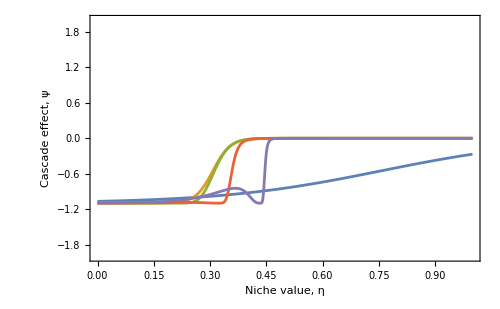

```mathematica
maxdist = 5;
ExpectedCascadeDistPlot=Show[
Table[
Plot[cascadevalue[[k]]/.Table[Subscript[η, j]->Subscript[η, i],{j,1, maxdist}],{Subscript[η, i],0,1},PlotRange->{-2,2},Filling->None,PlotStyle->ColorData[97,k],Frame->True,FrameLabel->{Style["Niche value, η",FontFamily->"Times New Roman",FontSize->18],Style["Cascade effect, ψ",FontFamily->"Times New Roman",FontSize->18]},LabelStyle->Directive[FontSize->16,Black]],{k,1,maxdist}],ImageSize->500
]
```

```mathematica
tlcascadesim = Import[StringJoin[$HomeDirectory,"/Dropbox/PostDoc/2024_trophicspinglass/trophicspinglass/data/tlcascadeC04.csv"]];
tlcascadesimdata =tlcascadesim [[2;;,All]];
```

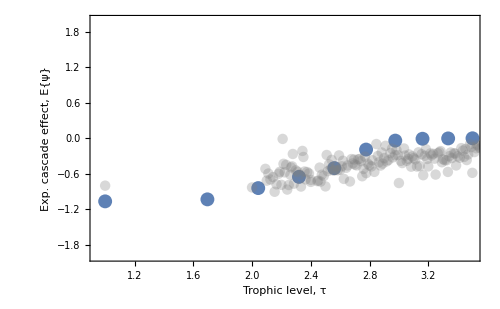

```mathematica
ExpectedCascadePlot=
Show[{
ListPlot[Transpose[{trophiclevels,ExpectedCascade}],PlotStyle->{ColorData[97,1],PointSize[0.02]},Joined->False,Frame->True,FrameLabel->{Style["Trophic level, τ",FontFamily->"Times New Roman",FontSize->18],Style["Exp. cascade effect, E{ψ}",FontFamily->"Times New Roman",FontSize->18]},PlotRange->{-2,2},LabelStyle->Directive[FontSize->16,Black],ImageSize->500],
ListPlot[tlcascadesimdata,PlotStyle->Directive[Opacity[0.3],Gray,PointSize[0.015]]]
}]
```

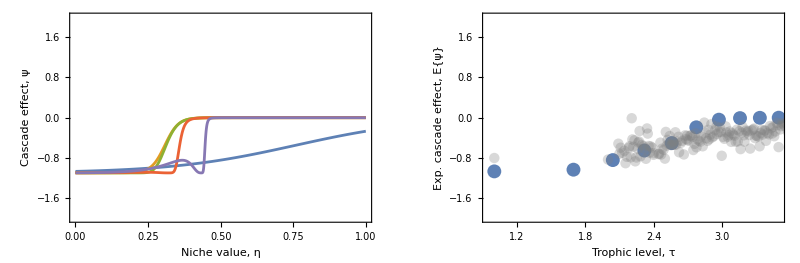

```mathematica
CascadePlot = GraphicsRow[{
ExpectedCascadeDistPlot,
ExpectedCascadePlot
},ImageSize->800]
```

```mathematica
filename = StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2024_trophicspinglass/trophicspinglass/figures_prefinal/fig_expectedcascade_C04.pdf"}];
Export[filename,CascadePlot];
```